```mathematica
Clear[ϵ]
```

```mathematica
(1/(50*365))/((1/(50*365))+1/7)
```

7/18257

```mathematica
S=(1/R)-(2p/((R-1)+√((R-1)^2+4*R*p)))
```

1/R-(2 p)/(-1+R+√((-1+R)^2+4 p R))

```mathematica
V=(ϵ*(R-1)+ϵ*√((R-1)^2+4*R*p))/(2*R)
```

((-1+R) ϵ+√((-1+R)^2+4 p R) ϵ)/(2 R)

```mathematica
ϵ=7/18257
```

7/18257

```mathematica
Solve[(1-R S+R V+ϵ)^2-4 (R V+ϵ-R S ϵ)==0,p]
```

{{p→1/(3477231583221888 R^2)(-10641263609375 R+11982137079444 R^2-1332199524222 R^3-5 √46646635 √(-15767767568014317125 R^2+47388103604191015608 R^3-47473044088764334500 R^4+15852708116880750000 R^5))},{p→1/(3477231583221888 R^2)(-10641263609375 R+11982137079444 R^2-1332199524222 R^3+5 √46646635 √(-15767767568014317125 R^2+47388103604191015608 R^3-47473044088764334500 R^4+15852708116880750000 R^5))}}

```mathematica
Clear[p]
```

```mathematica
g[R_]:=1/(3477231583221888 R^2)(-10641263609375 R+11982137079444 R^2-1332199524222 R^3+5 √46646635 √(-15767767568014317125 R^2+47388103604191015608 R^3-47473044088764334500 R^4+15852708116880750000 R^5))
```

```mathematica
h[R_]:=g[R+1]
```

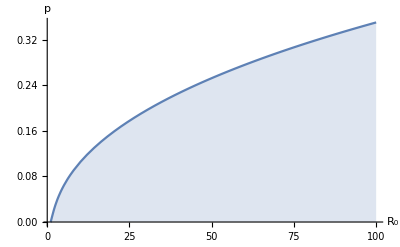

```mathematica
Plot[g[R],{R,0,100},Filling->Bottom,AxesLabel->{Subscript[R, 0],p},PlotRange->All]
```

Plot::invpr: Value of option PlotRange is not compatible with the option ScalingFunctions -> {{Log,Exp},{Identity,Identity}}

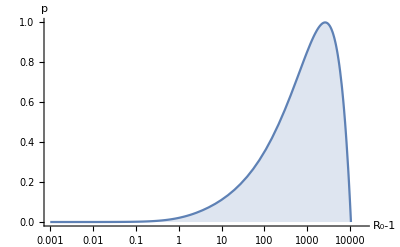

```mathematica
LogLinearPlot[h[R],{R,0.001,18000},Filling->Bottom,AxesLabel->{"R_0-1",p},PlotRange->{{0,20000},{0,1}}]
```

```mathematica
Show[%9,AxesLabel->{HoldForm[Subscript[R, 0]-1],p},PlotLabel->RawBoxes[RowBox[{RowBox[{"50"," ","years"," ","lifespan"}],","," ",RowBox[{"7"," ","days"," ","mean"," ","infectious"," ","period"}]}]],LabelStyle->{GrayLevel[0]}]
```

Show::gtype: Symbol is not a type of graphics.

Show[Null,AxesLabel→{R_0-1,p},PlotLabel→(50 years lifespan, 7 days mean infectious period),LabelStyle→{GrayLevel[0]}]

```mathematica
Export["C:\\Users\\Roger Zhang\\Documents\\GitHub\\RogerZhang\\July_2nd\\Figures\\p_vs_R_0\\50_7.pdf",%10,"PDF"]
```

C:\Users\Roger Zhang\Documents\GitHub\RogerZhang\July_2nd\Figures\p_vs_R_0\50_7.pdf